## Training a classifier for source attribution of campylobacteriosis

Campylobacter is a foodborne pathogen that is the largest  cause  of bacterial gastroenteritis in the developed world.

Campylobacter is a zoonotic pathogen hosted by several animals including cattle, chicken, sheep, pig or wild birds. Food products from these animals represent a risk of infection to humans which can develop campylobacteriosis. If someone is infected, it is important to determine the origin of infection, i.e. which type of food is resposible for the transmission to the infected patient. If the source is identified, the authorities may decide to call back certain foods from the market to prevent further infections.

The aim of this practical is to use genomic data for Campylobacter samples from five animal reservoirs (see Figure) to train a classifier so that infections in humans can be attributed to one of the five reservoirs. The ultimate goal is to use the classifier to determine the origin of Campylobacter samples isolated from infected humans. In the dataset to be used, each sample is characterised by seven housekeeping genes for Campylobacter. Each gene is coded by a set of numbers (alleles). In practice, each sample is characterised by a feature vector consisting of 7 integer numbers. 

The dataset contains Campylobacter samples isolated from humans and from animal reservoirs (cattle, chicken, sheep, pig and wild bird).  You will first deal with samples from animal reservoirs to train a classifier and test its performance. After that, you will be ready to attribute human isolates to food sources. 

Practical suggestions:

Make sure that you understand the analysis of the Iris flowers done in lectures before attempting this practical!

Names for new variables are normally suggested throughout the practical. This is done to be able to refer to such variables in forthcoming tasks of the practical. You are free to use other names but this might be confusing. In addition, the solutions to the practical provided later will use the suggested names and you might find useful to use the same names to compare.

-Graphics-
Image from Pérez-Reche,F.J.,Rotariu,O.,Lopes,B.S.et al. Mining whole genome sequence data to efficiently attribute individuals to source populations. Sci Rep 10,12124 (2020). https://www.nature.com/articles/s41598-020-68740-6

## Task 1

Download the dataset Campylobacter_MLST.csv from MyAberdeen

Import the data and assign it to a variable (e.g. data)

## Task 2

Examine the format of the dataset. For instance, use the function Take to see the 10 first instances and look at the dimensions of the dataset. As you will see, data is a list of lists. It can be thought as a table consisting of 8 columns and 1173 rows. The first column gives the category of each isolate and each row corresponds to a different isolate.

## Task 3

Look at the name of different categories in the dataset which are given in the first column for each instance (isolate). This can be done by DeleteDuplicates.

## Task 4

Since the isolates from food reservoirs are assumed to be the sources of human isolates, it makes sense to split the list data into two lists, one corresponding to human isolates and another for isolates from food reservoirs.  The resulting lists should have the same format (e.g. same number of columns) as data. More explicitly:

Create a sublist from data for human isolates. Refer to it as dataHuman.

Create a list containing the data for food reservoirs only. Refer to the new list as dataSources.

As usual when defining new lists or variables, check that they look like you expect them to look.

## Task 5

Use dataSources to define a list named sourcenames containing the name of the sources. This will be useful to explore the data below. Note that isolates from wild birds are labeled as WB.

## Task 6

In the forthcoming analysis, it will be useful to have a list with the name of features (genes). For the purposes of this practical, you can refer to the genes as “gene 1”, “gene 2”,... “gene 7”

```mathematica
featurename={"gene 1","gene 2","gene 3","gene 4","gene 5","gene 6","gene 7"}
```

{gene 1,gene 2,gene 3,gene 4,gene 5,gene 6,gene 7}

## Task 7

Separate the instances in dataSources by source. In order to achieve this task, you may want to go back to the Iris flowers classification example where a similar task was done.

## Task 8

The goal of the classifier to be trained in this practical will be to classify unseen isolates into food reservoirs. In order for classification to be accurate, we need a reasonable separation between different reservoirs in the feature space. The feature space in this case consists of 7 dimensions (each isolate is represented by a point in this space and its coordinates are the values taken by its 7 genes). 

Since the dimension of the feature space is larger than 3, it is difficult to visualise at once on a 2D screen. 

One possible way to do a preliminary exploration is to plot the alleles for pairs of genes (pairs of features) and pairs of sources. This can be done using the following scatterplot:

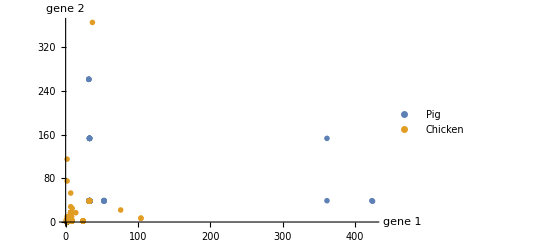

```mathematica
f1=1;
f2=2;
source1=4;
source2=3;
ListPlot[{bySources[[source1]][[All,{f1+1,f2+1}]],bySources[[source2]][[All,{f1+1,f2+1}]]},AxesLabel->featurename[[{f1,f2}]],PlotLegends->sourcenames[[{source1,source2}]],PlotMarkers->{"OpenMarkers", Medium},PlotRange->All]
```

Here, f1 and f2 correspond to features (genes). source1 and source2 correspond to two reservoirs.

In order to compare pairs of reservoirs, I suggest you proceed as follows:

Make sure you understand how the plot is made.

Systematically compare the scatterplot for pairs of sources and pairs of genes. The comparison between sources in this case is not as clear as the comparison between species in the Iris flowers problem. However, we can extract some preliminary conclusions. Which sources do you think are more different from each other? These are the ones that the classifier you will train later should identify more accurately.

## Task 9

In order to further analyse the data and try to confirm some of your conclusions in the previous task, plot a scatter plot matrix. In order to reduce the complexity of the scatter plot matrix, you may want to plot a reduced number of features (genes) at once.

## Task 10

To train a classifier with the source isolates and test its performance, you will need to define training and test datasets from the dataSources list.

In dataSources, there are some isolates that are identical (i.e. they share the same features). See, for instance the first 10 elements of the Tally counts in dataSources:

```mathematica
Take[Tally[dataSources],10]
```

{{{Cattle,2,1,5,3,725,1,5},2},{{Cattle,1,2,3,4,5,9,3},21},{{Cattle,19,24,23,20,26,16,15},8},{{Cattle,2,1,1,3,2,1,5},10},{{Cattle,1,4,2,2,6,3,17},18},{{Cattle,9,2,4,62,4,5,6},7},{{Cattle,1,1,59,2,10,5,7},5},{{Cattle,1,462,2,2,6,3,17},1},{{Cattle,2,1,5,3,2,1,5},19},{{Cattle,1,3,6,4,3,3,3},4}}

For instance, there are 8 isolates from cattle with the genotype {Cattle,19,24,23,20,26,16,15}.

Due to the repeated genotypes, to define training and test datasets you should select element numbers in lists, i.e. it is not as simple as what was done for the Iris plant example. For instance, to select 75% of the isolates from dataSources at random to define the training dataset, we proceed as follows:

First calculate the number of isolates corresponding to 75% of the total in dataSources. Let us refer to this quantity as ntrain.

Choose ntrain indices from the set {1,2,...,Length[dataSources]} at random for the training data. Let us refer to the resulting set of indices as indexTraindata.

Use the Complement function to define indices to be chosen from the original set to define the test dataset. Hint: This is the complement between a set of all the indices in dataSources and in indesTraindata.

Check that the intersection between indexTraindata and indexTestdata is null.

Use the indices indexTraindata and indexTestdata to define lists for training and testing from dataSources. I will refer to these as traindata and testdata, respectively.

Check that traindata and testdata look as you would expect (e.g. they have the right dimensions)

## Task 11

Use the Classify function with traindata to train a classifier for Campylobacter sources.

## Task 12

What classification method did Mathematica choose as the most accurate?

Display the learning curve for the classifier. In particular, look at the learning curve of different methods tested by Mathematica. Comment on the differences between methods.

## Task 13

Use the testdata list to obtain a ClassifierMeasurements object to test the performance of the classifier trained above.

## Task 14

Using the ClassifierMeasurements object obtained in the previous task, look at the following:

Accuracy of the classifier

Confusion matrix. Comment on the results (e.g. which are the less confused classes? which are the most confused classes? Is confusion symmetric among classes? Can confusion be understood in terms of your exploration of the data in previous tasks in terms of scatter plots?).

Calculate the true positive rate (TPR) for all the classes and plot the results in a bar chart with a bar for the TPR for each class (food reservoir). Comment on the meaning of TPR in this problem and discuss the results.

## Task 15

Look at the worst and best classified examples. Is there a clear trend that would allow us to conclude that the classification of isolates from some reservoirs is typically less accurate than other? To have a more complete view on this, you might find useful to create a table for sorted probabilities for each prediction.

## Task 16

Now that we have checked that a classifier for Campylobacter with the current dataset is reasonably accurate, we are in a position to attribute human isolates to sources. We expect that the accuracy of a classifier would increase with the number of isolates used to train it. Accordingly, it makes sense to use all the isolates in dataSources to train a new classifier to attribute human isolates.

Use all the source isolates in dataSources to train a new classifier.

## Task 17

Use the classifier found in Task 16 to classify the human isolates stored in dataHuman. Assign the results to a variable named as attribHuman.

## Task 18

Count the number of human isolates attributed to each source. Represent the fraction of human isolates attributed to each source in a bar chart. Describe the results in words.